# Classifying Cellular Automatons.

In this experiment, we will classify cellular automatons according to its underlying rules.

The Set

We will use the complete automaton range.

```mathematica
automat[n_] := RandomSample[Range[255],n]
```

```mathematica
SeedRandom[227019];
lAutomat = automat[10];
```

```mathematica
lAutomat = DeleteDuplicates@Append[lAutomat,110]
```

{167,11,129,215,88,32,237,156,173,236,110}

```mathematica
size = 32
```

32

We will use 25 samples per class.

```mathematica
nSamples = 25
```

25

```mathematica
SeedRandom[2602019]

TrainingSample = 
Catenate@Table[
Table[
With[{ini = RandomInteger[1,size]},
CellularAutomaton[
lAutomat[[i]], ini, size-1
]-> lAutomat[[i]]
]
,{i,Length[lAutomat]}
]
,{j,nSamples}];

ValidationSample = 
Catenate@Table[
Table[
With[{ini = RandomInteger[1,size]},
CellularAutomaton[
lAutomat[[i]], ini, size-1
]-> lAutomat[[i]]
]
,{i,Length[lAutomat]}
]
,{j,nSamples}];

TestSample  =
Catenate@Table[
Table[
With[{ini = RandomInteger[1,size]},
CellularAutomaton[
lAutomat[[i]], ini, size-1
]-> lAutomat[[i]]
]
,{i,Length[lAutomat]}
]
,{j,5*nSamples}];
```

A sample is:

```mathematica
(ArrayPlot[#[[1]]]-> #[[2]])&@TrainingSample[[1]]
```

-Graphics-→167

## Accuracy of Naive Neural Networks.

nn: Neural Network that takes in a flattened vector of 1s and 0s. (all timesteps in one go)

```mathematica
nn =  NetChain[{FlattenLayer[], 
LinearLayer[],
SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",lAutomat}],"Input"-> {size,size}];
```

```mathematica
net = NetTrain[nn,TrainingSample, All,ValidationSet-> ValidationSample,
MaxTrainingRounds->500,TargetDevice->{"GPU",2}]
```

NetTrainResultsObject[<>]

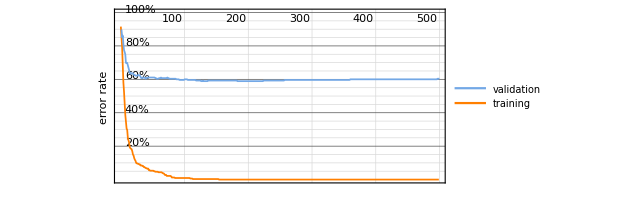

```mathematica
net["ErrorRateEvolutionPlot"]
```

```mathematica
ClassifierMeasurements[net["TrainedNet"],TestSample,"Accuracy"]
```

0.390545

```mathematica
ClassifierMeasurements[net["TrainedNet"], TrainingSample,"Accuracy"]
```

0.996364

So, even with this simple model, we have a textbook example of overfitting. The linear layer has enough variance to reach a 100% accuracy on the training set, but only manages a 0.28% accuracy on the test set.

```mathematica
nn2 =  NetChain[{FlattenLayer[], 
LinearLayer[size*size],
LinearLayer[],
SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",lAutomat}],"Input"-> {size,size}];
```

```mathematica
net2 = NetTrain[nn2,TrainingSample, All,ValidationSet-> ValidationSample,
MaxTrainingRounds->500,
TargetDevice->{"GPU",2}]
```

NetTrainResultsObject[<>]

```mathematica
ClassifierMeasurements[net2["TrainedNet"],TestSample,"Accuracy"]
```

0.395636

```mathematica
ClassifierMeasurements[net2["TrainedNet"], TrainingSample,"Accuracy"]
```

0.996364

We can see that Naive Neural Networks have low Accuracy on the problem.

### Final Neural Network.

```mathematica
nn3 =  NetChain[{FlattenLayer[], 
LinearLayer[size*size],
LinearLayer[size*size],
LinearLayer[],
SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",lAutomat}],"Input"-> {size,size}];
```

```mathematica
net3 = NetTrain[nn3,TrainingSample, All,ValidationSet-> ValidationSample,
MaxTrainingRounds->500,
TargetDevice->{"GPU",2}]
```

NetTrainResultsObject[<>]

```mathematica
ClassifierMeasurements[net3["TrainedNet"], TestSample,"Accuracy"]
```

0.396364

```mathematica
ClassifierMeasurements[net3["TrainedNet"], TrainingSample,"Accuracy"]
```

1.

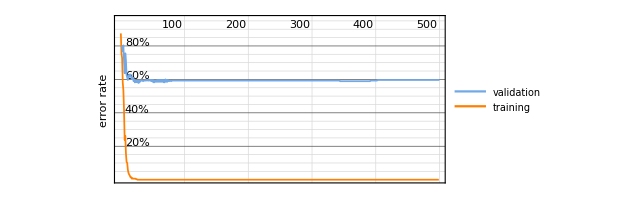

```mathematica
net3["ErrorRateEvolutionPlot"]
```

Another one.

```mathematica
nn4 =  NetChain[{FlattenLayer[], 
LinearLayer[size*size],
LinearLayer[size*size],
LinearLayer[size*size],
LinearLayer[],
SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",lAutomat}],"Input"-> {size,size}];
```

```mathematica
net4 = NetTrain[nn4,TrainingSample, All,ValidationSet-> ValidationSample,
MaxTrainingRounds->500,
TargetDevice->{"GPU",2}]
```

NetTrainResultsObject[<>]

```mathematica
ClassifierMeasurements[net4["TrainedNet"], TestSample,"Accuracy"]
```

0.397818

## The Performance of a Convolutional Deep Network.

The following Neural Network so far has shown excellent performance on this task.

```mathematica
nn =  NetChain[{ ConvolutionLayer[16,{3,2}],Ramp,PoolingLayer[{size-2,size-3}],FlattenLayer[], LinearLayer[Length@lAutomat],SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",lAutomat}],"Input"-> {1,size,size}];
```

We need to add one channel for this network to work.

```mathematica
TrainingSample2 = Map[{#[[1]]}->#[[2]]&,TrainingSample];
```

```mathematica
ValidationSample2=  Map[{#[[1]]}->#[[2]]&,ValidationSample];
```

```mathematica
TestSample2 =  Map[{#[[1]]}->#[[2]]&,TestSample];
```

```mathematica
SeedRandom[26022019]
net = NetTrain[nn,TrainingSample2,ValidationSet->ValidationSample2, TargetDevice->{"GPU",2}]
```

NetChain[<>]

```mathematica
ClassifierMeasurements[net, TestSample2, "Accuracy"]
```

0.989091

The accuracy is very good.

Now, given the requirements for the classifier that the input be of size 1xn...xn, we will define a second classifier to make the next code compatible.

```mathematica
compNet[x_] := net[{x}]
```

## Breaking the Network With Small Pixel Attacks.

Given a classifier and a sample, the following function will return a list of successful attacks.

```mathematica
flipPixelL[ls_,idx_]:=
ReplacePart[ls,idx-> If[
ls[[idx]]==0,1,0]
]
```

```mathematica
flipPixelS[sam_, idx_]:=With[
{
ogDim=Dimensions[sam[[1]]],
flat = Flatten[sam[[1]]]
},
With[
{
flipped =flipPixelL[flat,idx]},
 ArrayReshape[flipped,ogDim]-> sam[[2]]
]
]
```

```mathematica
(* flips all the pixels given in the list 'lIdx' *)
nflipPixelS[sam_, lIdx_]:= Fold[flipPixelS,sam,lIdx]
```

```mathematica
(* The function *)
pixelAttack[class_,sample_]:=Select[
Range[
Fold[#1*#2&,1,#]&@Dimensions[sample[[1]]]
],
class[flipPixelS[sample, #][[1]]]≠sample[[2]]&
]
```

Example of execution:

```mathematica
x = TestSample[[1]];
```

```mathematica
pixelAttack[compNet,x]
```

{42,73,93,124,155,217,248,279,341,372,403,465,496,527,589,620,651,713,744,775,837,868}

```mathematica
(* function that can do 'n' pixel attacks *)
```

```mathematica
npixelAttack[class_,sample_,nm_]:= With[
{cand = Subsets[
Range[Fold[#1*#2&,1,#]&@Dimensions[sample[[1]]]]
,{nm}]
},
Parallelize@Select[
cand,class[nflipPixelS[sample, #][[1]]]≠sample[[2]]&
]
]
```

```mathematica
(* npixelAttack[compNet,x,2] *)
```

Going through all the list is too computational expensive.

Expected Number of 1-Pixel attacks to break each Sample.

Let’s compute the expected number of 1-pixel attacks needed to break the prediction of a sample.

First, a sample of the test set, otherwise this is very expensive.

```mathematica
SeedRandom[02012019]
vSet = RandomSample[TestSample,1000];
```

Now, the experiment.

```mathematica
(* attacks = ParallelTable[
pixelAttack[compNet,vSet[[i]]]
,{i,Length[vSet]}
] *)
```

```mathematica
expected = N@(Total@ParallelTable[
Length@pixelAttack[compNet,vSet[[i]]]
,{i,Length[vSet]}]/Length[vSet])
```

140.64

140 per sample is a significant number.

## The Same Attack on our Algorithmic Classifier.

Let' s try the same attack on the classifier.Since we have no reason to believe that the same pixels will work, we will try to find another list.

The BDM function:

```mathematica
SetDirectory[NotebookDirectory[]]
```

F:\Dropbox\PostDoc\MathematicaNB\Classification\Breaking

```mathematica
reducedD2=<<"squares2Dsize1to4.m";
```

```mathematica
Table[With[{sq=reducedD2[[nS]]},HashSquares[sq[[1]]]=sq[[2]]],{nS,Length@reducedD2}];
```

```mathematica
Clear[reducedD2];
```

```mathematica
BDM[array_,dim_Integer:4]:=If[TrueQ[Min[Dimensions[array]]<dim],BDM[array,Min[Dimensions[array]]],First[Block[{part=Partition[array,{dim,dim}]},Total[{Log[2,#[[2]]]+#[[1]]}&/@({HashSquares[#[[1]]],#[[2]]}&/@Tally[Flatten[part,1]])]]]]
```

## Conditional BDM.

Functions to parse through shared members.

```mathematica
Clear[NotIn]
```

```mathematica
NotIn[List[],rep_]:= List[]
```

```mathematica
NotIn[x_,rep_]:=If[MemberQ[rep,x[[1]]],NotIn[x[[2;;]],rep],Prepend[NotIn[x[[2;;]],rep],x[[1]]]]
```

```mathematica
Shrd[List[],rep_]:=List[]
```

```mathematica
Shrd[x_,rep_]:= If[MemberQ[rep,x[[1]]],Prepend[Shrd[x[[2;;]],rep],x[[1]]],Shrd[x[[2;;]],rep]]
```

#### Conditional Squared BDM Function.

```mathematica
Clear[BDMC]
```

```mathematica
BDMC[array_,array2_,dim_Integer, offset_:dim_Integer]:=
If[TrueQ[Min[Dimensions[array]]<dim],
BDMC[array,array2,Min[Dimensions[array]]],

Block[{
part=Catenate[Partition[array,{dim,dim},{offset,offset}]],
part2= Catenate[Partition[array2, {dim,dim},{offset,offset}]]
},
  Total[(HashSquares[#[[1]]]+Log[2,#[[2]]])&/@Tally[NotIn[part, part2]]] +
	Total[Log[2,#[[2]]]&/@Tally[Shrd[part, part2]]]
]
]
```

Training the Classifier.

```mathematica
lossM[c_,x_]:=BDMC[x[[1]],c,4,1]^2
```

```mathematica
costM[c_,set_]:= N@Total[
lossM[c,#]&/@set
]
```

```mathematica
getClass[n_, set_]:= getClass2[n,set,Length[set],List[]]

getClass2[n_,set_,i_, acc_]:=If[
i>0,
getClass3[n, set, i, acc],
Return[acc]
]

getClass3[n_,set_,i_, acc_]:=If[
n==set[[i]][[2]],
getClass2[n,set,i-1, Append[acc,set[[i]]]],
getClass2[n,set,i-1, acc]
]
```

```mathematica
(* needed for my program to work *)
$RecursionLimit=Infinity;
$IterationLimit=Infinity;
CloseKernels[];
ParallelEvaluate[$RecursionLimit=Infinity;$IterationLimit=Infinity,LaunchKernels[8]];
```

```mathematica
Table[
partitions[lAutomat[[i]]]= 
Catenate@Catenate@(
Partition[#,{4,4},{1,1}]&/@Keys@getClass[lAutomat[[i]],TrainingSample]
)
,{i,Length[lAutomat]}
];
```

Let’s make it unique.

```mathematica
Table[
partitions[lAutomat[[i]]]=#[[1]]&/@Tally@partitions[lAutomat[[i]]]
,{i,Length[lAutomat]}
];
```

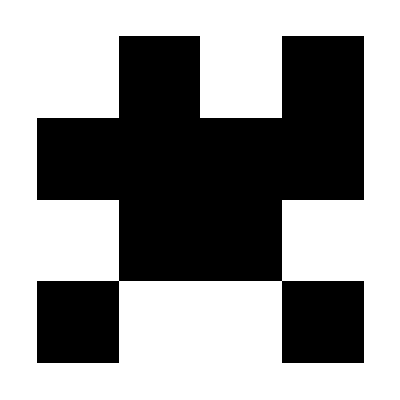
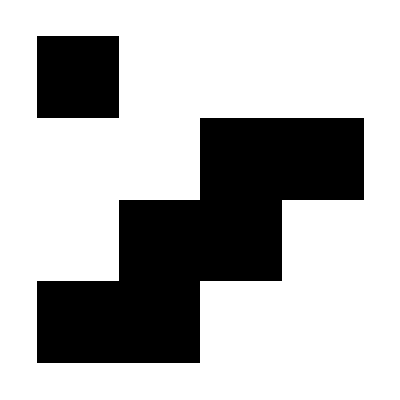
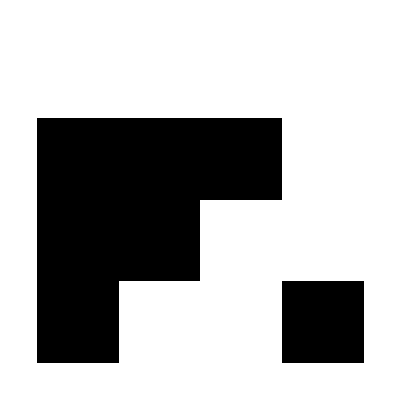
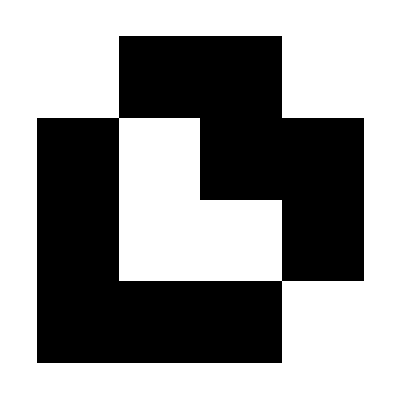
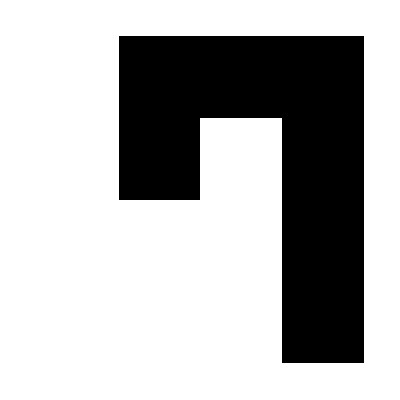
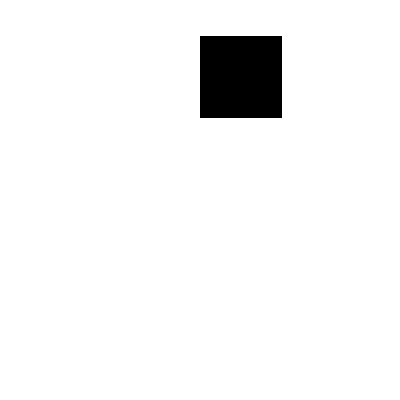
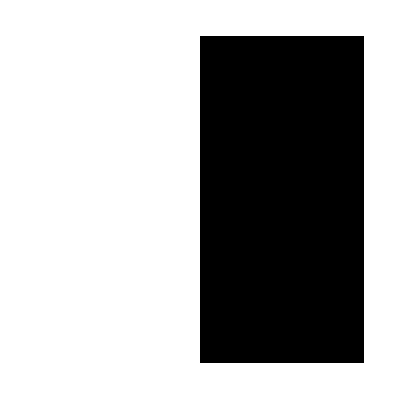
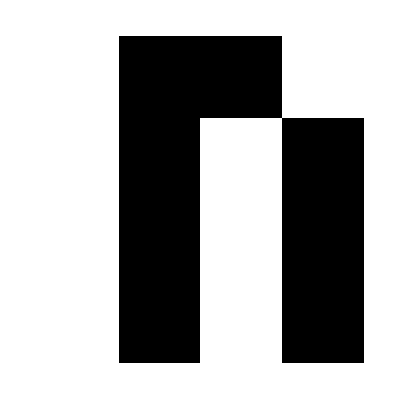

```mathematica
(* firstM = lAutomat;
SetSharedVariable[firstM]
 *)
ArrayPlot/@Table[
With[
{
aut = lAutomat[[i]],
set = getClass[lAutomat[[i]],TrainingSample],
search = partitions[lAutomat[[i]]]
},
firstM[aut]=  MinimalBy[
search,
costM[#, set]&,1
][[1]]
]
,{i,Length[lAutomat]}
]
```

Function to iterate the previous code.

First, some helper functions.

```mathematica
(*  Function that constructs an square matrix of matrices *)
consTM[lm_]:=With[
{nRows = Sqrt[Length[lm]]},
With[
{rows = Partition[lm,nRows]},
Catenate[joinRow/@rows]
]
]

joinRow[rs_]:= joinRow2[Rest[rs],rs[[1]],Length[rs]-1]

joinRow2[rs_, acc_, n_]:= If[n==1,
Join[acc,rs[[1]],2],
joinRow2[Rest[rs],Join[acc,rs[[1]],2],n-1]
]
```

```mathematica
(* Given the list of current matrices, it generates a new matriz with a padding of zeros*)
newMat[act_, ins_,nm_]:=
With[
{
pad=ConstantArray[
ConstantArray[0,Dimensions[ins]],nm-Length[act]-1]
},
consTM[
Join[Append[act,ins],pad]
]
]
```

Now, the training algorithm.

```mathematica
(* Given and Initial matrix, adds the next matrix that minimizes the loss function *)
```

```mathematica
trainNext[cs_,search_,set_]:=
With[
{nextM = MinimalBy[
search,
costM[newMat[cs,#,16],set]&,1
][[1]]},
Append[cs,nextM]
]
```

First, we need to set the recursion limit on all the kernels.

```mathematica
(* SetSharedVariable[lAutomat,TrainingSample]; 
$SharedVariables *)
```

```mathematica
mats =ParallelTable[
With[
{
aut = lAutomat[[i]],
set = getClass[lAutomat[[i]],TrainingSample],
search = partitions[lAutomat[[i]]]
},
Nest[trainNext[#,search,set]&,{firstM[aut]},15]
]
,{i,Length[lAutomat]}];
```

And the matrices chosen are (Lets put them in the model)

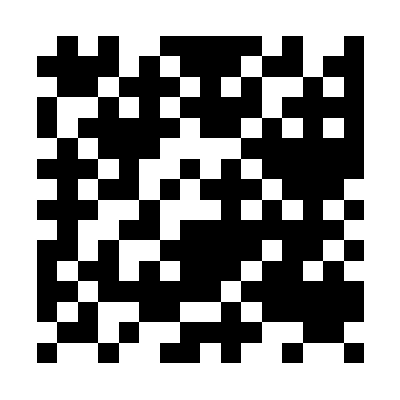
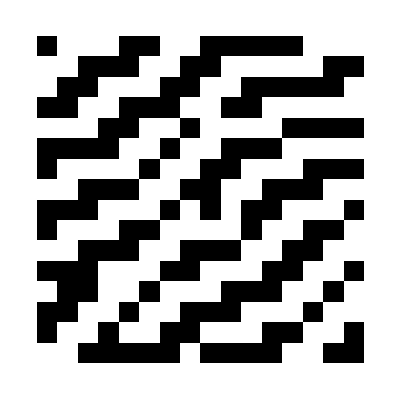
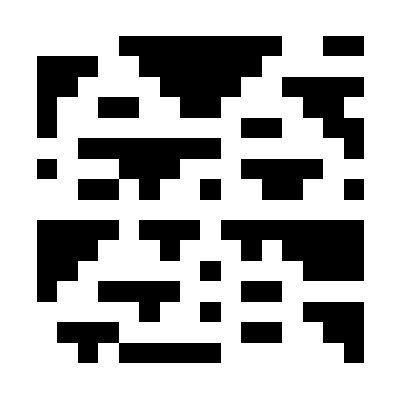
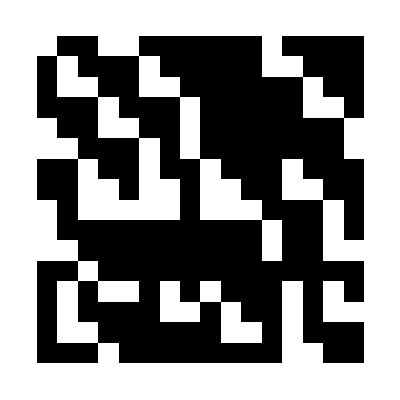
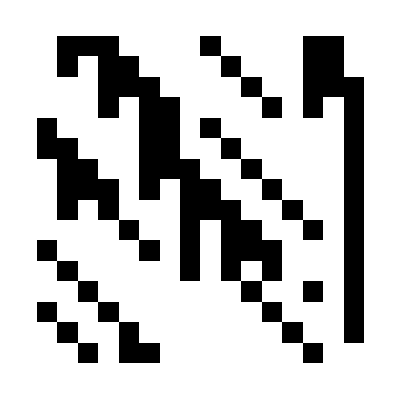
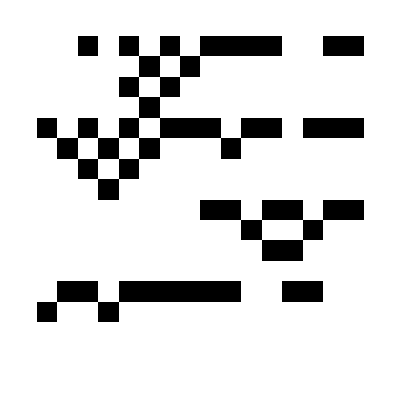
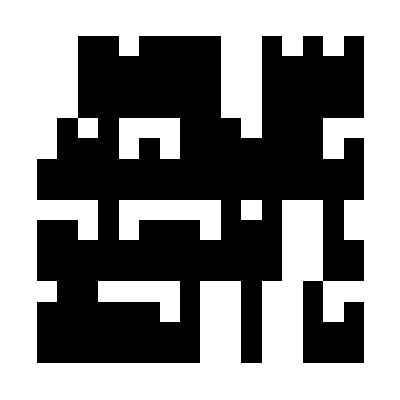
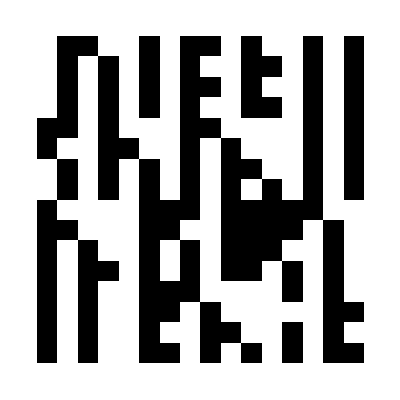

```mathematica
ArrayPlot/@Table[Model[lAutomat[[i]]]=consTM[mats[[i]]],{i,Length@lAutomat}]
```

```mathematica
pred[M_,x_]:=
Quiet@MinimalBy[lAutomat, BDMC[x,M[#],4,1]&][[1]]
```

```mathematica
right = 0;
wrong = List[]
Table[
If[
pred[
Model, TestSample[[i]][[1]]
]== TestSample[[i]][[2]],
right = right +1,
wrong=Append[wrong,TestSample[[i]]]
]
,{i,Length[TestSample]}];
```

{}

```mathematica
right
```

1349

And the accuracy is:

```mathematica
N@right/Length[TestSample]
```

0.981091

Which is lower than the perfect 100%, but still decent I believe.

```mathematica
Model[lAutomat[[1]]]
```

{{0,1,0,1,0,0,1,1,1,1,1,0,1,0,0,1},{1,1,1,1,0,1,0,1,1,1,0,1,1,0,1,1},{0,1,1,0,1,1,1,0,1,0,1,0,0,1,0,1},{1,0,0,1,0,1,0,1,1,1,1,0,1,1,1,1},{1,0,1,1,1,1,1,0,1,1,0,1,0,1,0,1},{0,1,0,1,1,1,0,0,0,0,1,1,1,1,1,1},{1,1,1,0,1,0,0,1,0,1,0,1,1,1,1,1},{0,1,0,1,1,0,1,0,1,1,1,0,1,1,1,0},{1,1,1,0,0,1,0,0,0,1,0,1,0,1,0,1},{0,1,0,0,1,1,0,1,1,1,1,1,1,1,1,0},{1,1,0,1,0,0,1,1,1,1,1,0,1,1,0,1},{1,0,1,1,0,1,0,1,1,1,0,1,1,0,1,0},{1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1},{1,0,1,0,0,1,1,0,0,1,0,1,1,1,1,1},{0,1,1,0,1,0,0,1,1,1,1,0,0,1,1,0},{1,0,0,1,0,0,1,1,0,1,0,0,1,0,0,1}}

Attacking the Model.

```mathematica
expected2 = N@(Total@ParallelTable[
Length@pixelAttack[pred[Model,#]&,TestSample[[i]]]
,{i,5}]/5)
```

11.

11 per sample is a significant number is much lower than 140.